```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
A={{1,0,0},{0,0,1},{1/2,1/2,1/2}};
```

```mathematica
B= Inverse[Transpose[A] ]
```

{{1,-1,0},{0,-1,1},{0,2,0}}

```mathematica
b=Sort[Transpose[Tally[Flatten[Table[Table[Table[Norm[h B[[1]]+k B[[2]]+l B[[3]]],{h,-5,5}],{k,-5,5}],{l,-5,5}],3]]][[1]],#1<#2&][[2;;5]]
```

{√2,2,√6,2 √2}

```mathematica
T=2 ArcSin[x/2*b]/Pi*180;
```

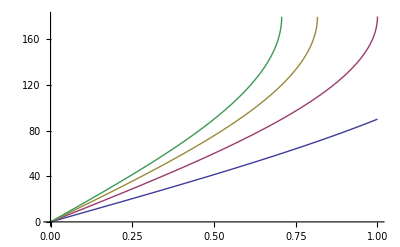

```mathematica
Plot[{T},{x,0,1}]
```

```mathematica
Solve[T[[1]]==28.8,x]
T/.%
```

{{x→0.351701}}

{{28.8,41.1827,51.0295,59.6536}}